```mathematica
f[x_]:=Exp[-(x-2)^2]+Exp[-(x-4)^2]
```

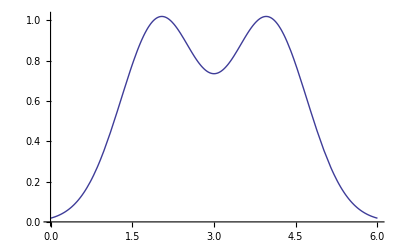

```mathematica
Plot[f[x],{x,0,6}]
```

```mathematica
RevolutionPlot3D[f[x],{x,1,5},RevolutionAxis->{1,0,0}]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[f[x],{x,1,5},RevolutionAxis->{0,0,1}]
```

-Graphics3D-

```mathematica
Exit[]
```

```mathematica
P[n_]:=Module[{},Do[If[PrimeQ[a],Print[a]],{a,1,n-1}]]
P[35]
```

2

3

5

7

11

13

17

19

23

29

31

```mathematica
For[i=1,i<10,i++,Print[i]]
```

1

2

3

4

5

6

7

8

9

```mathematica
fib[n_]:=Module[{},f[1]=1;f[2]=1;f[i_]:=f[i]=f[i-2]+f[i-1];f[n]]
fib[5]
```

5

```mathematica
Lpp[n_]:=Module[{},For[i=1,Prime[i]<n,i++,Print[Prime[i]]]]
Lpp[9]
```

2

3

5

7

```mathematica
Lpp2[n_]:=Module[{},For[i=1,i<n,i++,If[PrimeQ[i],Print[i]]]]
Lpp2[9]
```

2

3

5

7

```mathematica
Lpp3[n_]:=Module[{},i=1;While[i<n,If[PrimeQ[i],Export["Nirab.txt",i]];i++]]
Lpp3[90]
```

```mathematica
Export["Nirab.dat",Lpp3[100]]
```

2

3

5

7

11

13

17

19

23

29

31

37

41

43

47

53

59

61

67

71

73

79

83

89

97

Nirab.dat

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Nirab.dat"]]]
```

```mathematica
Exit[]
```

```mathematica
g[x_,y_]:=4-x^2-y^2
f[r_,t_]=Simplify[g[r*Cos[t],r*Sin[t]]]
```

4-r^2

```mathematica
ContourPlot3D[z==g[x,y],{x,-2,2},{y,-2,2},{z,0,4}]
```

-Graphics3D-

```mathematica
ContourPlot3D[z==f[r,t],{r,-2,2},{t,-Pi,Pi},{z,0,4}]
```

-Graphics3D-

```mathematica
volume=Integrate[4-r^2,{t,0,2Pi},{r,0,2}]
```

(32 π)/3